## Toy example to illustrate MIMO loop shaping (Section 3.8.4)

```mathematica
Clear["Global`*"]
```

```mathematica
G0 =( 1/(1+s+s^2))({{2, -2}, {-1, 2}})
```

{{2/(1+s+s^2),-2/(1+s+s^2)},{-1/(1+s+s^2),2/(1+s+s^2)}}

```mathematica
K0 = (1+1/s) G0 // Simplify
```

{{(2+2 s)/(s+s^2+s^3),-(2 (1+1/s))/(1+s+s^2)},{-(1+s)/(s+s^2+s^3),(2+2 s)/(s+s^2+s^3)}}

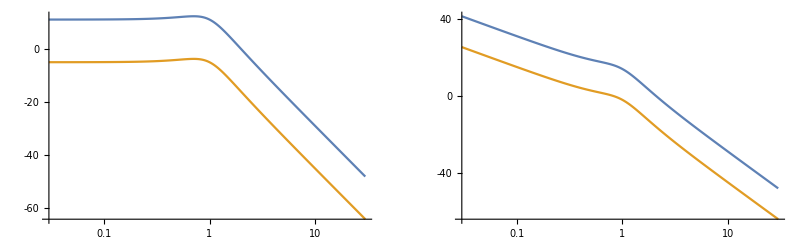

```mathematica
p1=SingularValuePlot[G0,{0.03,30}];
p2=SingularValuePlot[K0,{0.03,30}];
GraphicsRow[{p1,p2}]
```